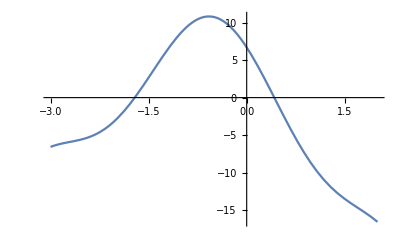

```mathematica
f[x_]:=5Cos[2x+1]-3 x^2-5x+4
Plot[f[x], {x,-3,2}]
```

```mathematica
g[x_]:=(Cos[2x+1]-3 x^2+4)/5
```

```mathematica
x=1;
e=0.001;
Do[
x1=x;
x=g[x]//N;
If[Abs[x1-x]<e,
Print["Решение x =", x//N, "получено на шаге ", i, "шаге"];
Break[]],
{i,1,100}]
```

General::ovfl: Overflow occurred in computation.